```mathematica
(*Solution to finite duration LZ Model*)
```

## Numerics

```mathematica
Δ=1.;
GroundStateInitial=1+0I;
ExcitedStateInitial=0 + 0 I;
```

```mathematica
CoeffList={};
For[T=10^-16, T≤1, T+=0.001, {z=NDSolveValue[{x''[t]==(2I/T -Δ^2 - (2 t / T)^2)x[t], x[-T/2]==GroundStateInitial, x'[-T/2]==-I(GroundStateInitial + Δ ExcitedStateInitial)}, x, {t, -T/2, T/2}]; AppendTo[CoeffList, z[T/2]]}];
```

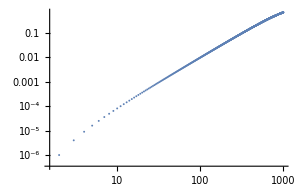

```mathematica
ListLogLogPlot[1-Abs[CoeffList]^2]
```

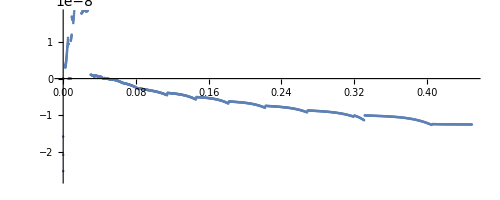

```mathematica
ComplexListPlot[1-CoeffList]
```